# Point Force Greens Functions (force)

```mathematica
r = Sqrt[(x-xs)^2 +(y-ys)^2];
Upt =1/2/Pi*Log[r]
s12 = D[Upt,x]
s13 = D[Upt,y]
```

Log[√((x-xs)^2+(y-ys)^2)]/(2 π)

(x-xs)/(2 π ((x-xs)^2+(y-ys)^2))

(y-ys)/(2 π ((x-xs)^2+(y-ys)^2))

## Integration over a constant source defined from y in [-W,W]

```mathematica
Uconst = Integrate[Upt,ys,GeneratedParameters->C]
Uconst1d =ReplaceAll[Uconst,{ys->w,xs->0}]-ReplaceAll[Uconst,{ys->-w,xs->0}]//FullSimplify
```

C[1]+(-2 ys-2 (x-xs) ArcTan[(y-ys)/(x-xs)]-(y-ys) Log[(x-xs)^2+(y-ys)^2])/(4 π)

(-4 w+2 x (ArcTan[(w-y)/x]+ArcTan[(w+y)/x])+(w-y) Log[x^2+(w-y)^2]+(w+y) Log[x^2+(w+y)^2])/(4 π)

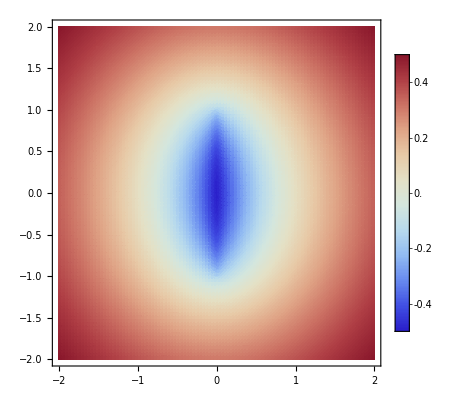

```mathematica
DensityPlot[ReplaceAll[Uconst1d,{w->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->BarLegend[{Automatic,{-0.5,0.5}}],PlotPoints->100,PlotRange->{-0.5,0.5}]
```

## Integrate point source with linear force function over the domain y in [-W,W]

```mathematica
Ulin = Integrate[Upt*(a0+a1*ys),ys,GeneratedParameters->C]
Ulin1d =ReplaceAll[Ulin,{ys->w,xs->0}]-ReplaceAll[Ulin,{ys->-w,xs->0}]//FullSimplify
```

C[1]+1/(8 π)(-ys (4 a0+a1 (2 y+ys))-4 (x-xs) (a0+a1 y) ArcTan[(y-ys)/(x-xs)]+(2 a0 (-y+ys)+a1 (x^2-2 x xs+xs^2-y^2+ys^2)) Log[x^2-2 x xs+xs^2+(y-ys)^2])

1/(8 π)(-4 w (2 a0+a1 y)+4 x (a0+a1 y) ArcTan[(w-y)/x]+4 x (a0+a1 y) ArcTan[(w+y)/x]+(2 a0 (w-y)+a1 (w^2+x^2-y^2)) Log[x^2+(w-y)^2]+(2 a0 (w+y)-a1 (w^2+x^2-y^2)) Log[x^2+(w+y)^2])

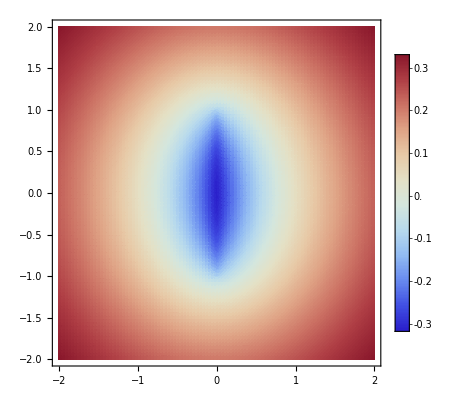

```mathematica
DensityPlot[ReplaceAll[Ulin1d,{w->1,a0->1,a1->0}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->{-1,1},PlotPoints->100,PlotRange->{-0.5,0.5}]
```

```mathematica
S12 = D[Ulin1d,x]//FullSimplify
S13 = D[Ulin1d,y]//FullSimplify
```

(2 (a0+a1 y) ArcTan[(w-y)/x]+2 (a0+a1 y) ArcTan[(w+y)/x]+a1 x (Log[x^2+(w-y)^2]-Log[x^2+(w+y)^2]))/(4 π)

(-4 a1 w+2 a1 x ArcTan[(w-y)/x]+2 a1 x ArcTan[(w+y)/x]-(a0+a1 y) (Log[x^2+(w-y)^2]-Log[x^2+(w+y)^2]))/(4 π)

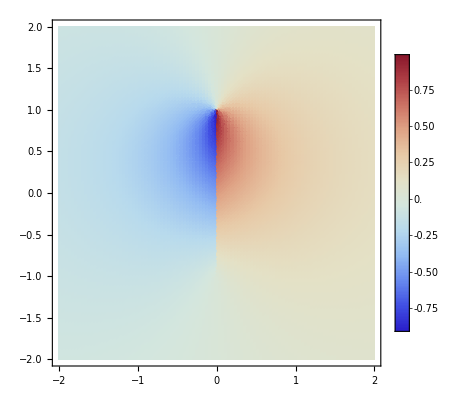

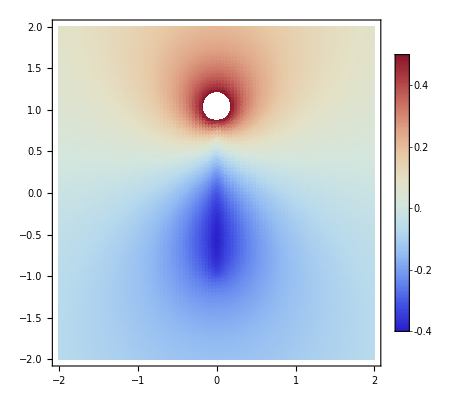

```mathematica
DensityPlot[ReplaceAll[S12,{w->1,a0->1,a1->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100]
DensityPlot[ReplaceAll[S13,{w->1,a0->1,a1->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->100,PlotRange->{-0.5,0.5}]
```